```mathematica
(*
k1=-1.003664013127360 10^-2;
k2=2.194720476205664 10^+0;
k3=3.622177244599267 10^-4;
k4=4.306784511138259 10^-2;
k5=-4.712794643730906 10^+0;
k6=1.293228142971838 10^-2;
k7=-6.928742017897364 10^-1;
k8=-3.105948102428563 10^-2;
k9=3.635396623498841 10^+0;
k10=-5.577595543405037  10^-3;


k1=-9.096261296524362 10^-04;
k2=1.563390717760689 10^-01;
k3=5.510294165871715 10^-03;
k4=2.826155249085411 10^-03;
k5=-8.112831025380142 10^-01;
k6=-1.103377090795027 10^-02;
k7=-4.901114339562490 10^-02;
k8=-5.462208655918772  10^-03;
k9=1.509736176781744 10^+00;
k10=7.988321379653943 10^-03;

k1=-2.889794474058519 10^-03;
k2=-1.208588285296162 10^-03;
k3=2.201958629842505 10^-02;
k4=6.485109124883191 10^-04;
k5=-1.438489270702308 10^-01;
k6=-5.606362926467791 10^-02;
k7=-2.113643897117244 10^-02;
k8=-1.498834589367169 10^-03;
k9=7.690082703437420 10^-01;
k10=4.765072206264760 10^-02;*)

k1=-6.306319442659312 10^-04;
k2=-1.640168709495793 10^-03;
k3=3.962017072440235 10^-03;
k4=-2.887048260782111 10^-04;
k5=-1.412276545356571 10^-01;
k6=-7.931822230064153 10^-03;
k7=-2.104555700820865 10^-02;
k8=6.238774627110503 10^-04;
k9=7.651613620676274 10^-01;
k10=4.980440898351878 10^-03;
```

0.00070702-0.0271608 Cos[theta]+0.0270946 Cos[2 theta]-0.000593419 Cos[3 theta]+0.659139 Sin[theta]-0.845464 Cos[theta] Sin[theta]+0.0760877 Sin[3 theta]

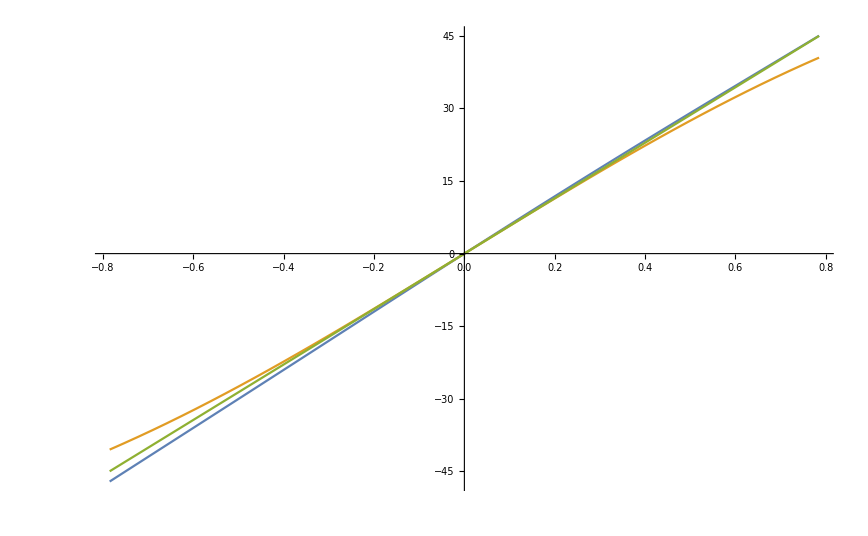

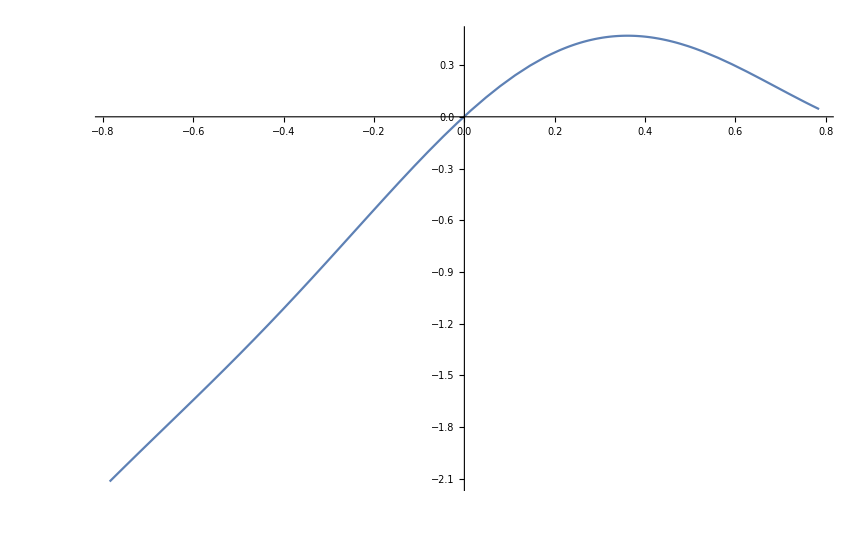

```mathematica
Y=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
X=(r0+xs)Cos[theta]+ys Sin[theta]-xd;
xs=0.0;
ys=0.10;
xd=0.0;
r0=2.4;
arctg=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;
Simplify[TrigReduce[arctg-Sin[theta]]]
Plot[{(arctg)*180/Pi,Sin[theta]*180/Pi,theta*180/Pi},{theta,-Pi/4,Pi/4}]
Plot[(arctg-theta)*180/Pi,{theta,-Pi/4,Pi/4}]
```

```mathematica
xs=0.0;
ys=0.0;
xd=0.0;
r0=2.4;
Y=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
X=(r0+xs)Cos[theta]+ys Sin[theta]-xd;
arctgbrez=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;
Simplify[TrigReduce[100 (arctgbrez-Sin[theta])]]
```

1.81878-2.65725 Cos[theta]+0.961384 Cos[2 theta]-0.11817 Cos[3 theta]+61.2519 Sin[theta]-81.3471 Cos[theta] Sin[theta]+6.7065 Sin[3 theta]

```mathematica
xs=0.10;
ys=0.0;
xd=0.0;
r0=2.4;
Y=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
X=(r0+xs)Cos[theta]+ys Sin[theta]-xd;
arctg=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;
Simplify[TrigReduce[100 (arctg-Sin[theta]-arctgbrez)]]
```

-1.66796+6.49478 Cos[theta]-1.66796 Cos[2 theta]+0.858597 Cos[3 theta]-100.095 Sin[theta]-3.35952 Cos[theta] Sin[theta]-0.0947641 Sin[3 theta]

```mathematica
xs=0.0;
ys=0.10;
xd=0.0;
Y=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
X=(r0+xs)Cos[theta]+ys Sin[theta]-xd;
arctg=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;
Simplify[TrigReduce[100(arctg-Sin[theta]-arctgbrez)]]
```

-1.74808-0.0588281 Cos[theta]+1.74808 Cos[2 theta]+0.0588281 Cos[3 theta]-95.338 Sin[theta]-3.19929 Cos[theta] Sin[theta]+0.902266 Sin[3 theta]

```mathematica
xs=0.0;
ys=0.0;
xd=0.10;
Y=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
X=(r0+xs)Cos[theta]+ys Sin[theta]-xd;
arctg=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;
Simplify[TrigReduce[100(arctg-Sin[theta]-arctgbrez)]]
```

-5.7782+3.18618 Cos[theta]-1.72493 Cos[2 theta]-96.7973 Sin[theta]+0.222206 Cos[theta] Sin[theta]